# Aero Components

## General

```mathematica
<<C:\\Hopsan\Compgen\CompgenNG02.mx
```

```mathematica
defaultPath=ToFileName[{"C:","HopsanTrunk","HOPSAN++","ComponentLibraries","defaultLibrary","Special","AeroComponents"}];
```

## Fuel Tank

```mathematica
domain = "Aero";
displayName = "FuelTank";
brief = "Calulates the mass of remaining fuel in tank";
componentType = "ComponentQ";
author = "Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[]
```

```mathematica
inputParameters  = {
   {massfuel0, 0., double, "kg/s", "The intitial fuel mass"}
   };
```

```mathematica
inputVariables  = {
   {massflow, 0., double, "kg/s", "Mass flow rate"}
   };
```

```mathematica
outputVariables  = {
   {massfuel, 0., double, "kg", "Fuel mass"},
   {consfuel, 0., double, "kg", "Consumed fuel mass"}
   };
```

```mathematica
systemEquationsDA = {
   Der[consfuel] == massflow
   };
```

```mathematica
systemVariables = {consfuel};
```

```mathematica
expressions = {
  		massfuel == limit[massfuel0 - consfuel, 0., massfuel0]
  		}
```

{massfuel==limit[-consfuel+massfuel0,0.,massfuel0]}

```mathematica
{{massfuel, limit[-consfuel + massfuel0, 0., massfuel0]}}
```

{{massfuel,limit[-consfuel+massfuel0,0.,massfuel0]}}

```mathematica
variableLimits = {{consfuel, 0, massfuel0}}
```

{{consfuel,0,massfuel0}}

```mathematica
{{consfuel, 0, massfuel0}}
```

{{consfuel,0,massfuel0}}

```mathematica
Compgen[file]
```

Part::partd: Part specification delayedPart ⟦ 1, 1 ⟧ is longer than depth of object.

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "AeroFuelTank", "displayname" → "AeroFuelTank"}, {XMLElement["icon", {"isopath" → "AeroFuelTank.svg", "iconrotation" → "ON", "userpath" → "AeroFuelTank.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → 0.5, "y" → "0", "a" → "90", "name" → "massflow"}, {}], XMLElement["portpose", {"x" → "0.333333", "y" → "1", "a" → "90", "name" → "massfuel"}, {}], XMLElement["portpose", {"x" → "0.666667", "y" → "1", "a" → "90", "name" → "consfuel"}, {}]}]}] in XMLElement["hopsanobjectappearance", {"version" → "0.1"}, XMLElement["modelobject", {"typename" → "AeroFuelTank", "displayname" → "AeroFuelTank"}, {XMLElement["icon", {"isopath" → "AeroFuelTank.svg", "iconrotation" → "ON", "userpath" → "AeroFuelTank.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → 0.5, "y" → "0", "a" → "90", "name" → "massflow"}, {}], XMLElement["portpose", {"x" → "0.333333", "y" → "1", "a" → "90", "name" → "massfuel"}, {}], XMLElement["portpose", {"x" → "0.666667", "y" → "1", "a" → "90", "name" → "consfuel"}, {}]}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "x" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

AeroFuelTank.xml

## Jet Engine

```mathematica
domain="Aero";
displayName="JetEngine";
brief="Calulates the mass of remaining fuel in tank";
componentType="ComponentQ";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[]
```

```mathematica
inputVariables={
{uin,1.,double,"","Throttle setting 0-1"},
{rho,1.25,double,"kg/m3","The density at altitude h"},{T,273.,double,"K","Temperature at altitude h"},{p0,100000.,double,"Pa","Pressure at altitude h"},{Vsound,340.,double,"m/s","Speed of sound at altitude h"},
{speed,100.,double,"m/s","Air speed"}
};
```

```mathematica
inputParameters={
{thrustmax,5000.,double,"N","Max thrust"},{SFC,0.0000171 ,double,"kg/(N s)","Nominal thrust specific fuel consumption"},
{BR,2,double,"","Bypass ratio"},
{thau,5.,double,"s","Engine time constant"},{Cspeed,1.,double,"","thrust-speed coefficient"}
};
```

```mathematica
outputVariables={
{thrust,5000.,double,"N","Thrust"},
{mfuel,0.,double,"kg","Burnt fuel amount"},{Shspeed,1.,double,"rad/s","Engine shaft speed"},{qmfuel,1.,double,"kg/s","Fuel, mass flow"}
};
```

```mathematica
rho0=1.25;
```

```mathematica
thruste0=(thrustmax*uin)/(thau s+1)
```

(thrustmax uin)/(1+s thau)

```mathematica
systemEquationsDA={
thrust==thruste0 rho/rho0,
mfuel==qmfuele/s
};
```

```mathematica
systemVariables={thrust,mfuel};
```

```mathematica
Shspeede=Cspeed*thrust
```

Cspeed thrust

```mathematica
qmfuele=SFC*thrust
```

SFC thrust

```mathematica
expressions={
Shspeed==Shspeede,
qmfuel==qmfuele
};
```

```mathematica
Compgen[file]
```

Part::partd: Part specification delayedPart ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification delayedPart ⟦ 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "AeroJetEngine", "displayname" → "A" … "ne"}, {XMLElement["icon", {"isopath" → "AeroJetEngine.svg", "iconrotation" → "ON", "userpath" → "AeroJetEngine.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → 0.142857, "y" → "0", "a" → "90", "name" → "uin"}, {}], XMLElement["portpose", {"x" → 0.285714, "y" → "0", "a" → "90", "name" → "rho"}, {}], « 6 », XMLElement["portpose", {"x" → "0.6", "y" → "1", "a" → "90", "name" → "Shspeed"}, {}], XMLElement["portpose", {"x" → "0.8", "y" → "1", "a" → "90", "name" → "qmfuel"}, {}]}]}] in XMLElement["hopsanobjectappearance", « 1 », XMLElement["modelobject", {"t" … "me" → "" … "", « 1 »}, {XMLElement["icon", {"isopath" → "AeroJetEngine.svg", "iconrotation" → "ON", "userpath" → "AeroJetEngine.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → 0.142857, "y" → "0", "a" → "90", "name" → "uin"}, {}], XMLElement["portpose", {"x" → 0.285714, "y" → "0", "a" → "90", "name" → "rho"}, {}], « 6 », XMLElement["portpose", {"x" → "0.6", "y" → "1", "a" → "90", "name" → "Shspeed"}, {}], XMLElement["portpose", {"x" → "0.8", "y" → "1", "a" → "90", "name" → "qmfuel"}, {}]}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.142857 in "x" → 0.142857 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.285714 in "x" → 0.285714 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.428571 in "x" → 0.428571 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

AeroJetEngine.xml

## Propeller

```mathematica
domain="Aero";
displayName="Propeller";
brief="Model of a propeller";
componentType="ComponentC";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[]
```

```mathematica
inputVariables={
{Up,1.25,double,"m/s","Air speed"},
{rho,1.25,double,"kg/m3","Air density"}
};
```

```mathematica
inputParameters={
{dp,1.,double,"m","Propeller diameter"},
{b1,0.2,double,"m","Propeller thrust coefficient"},
{b2,0.2,double,"m","Propeller thrust coefficient"},
{g1,0.205,double,"m","Propeller torque coefficient"},
{g2,0.2,double,"m","Propeller torque coefficient"},
{ct0,0.12,double,"m","Propeller torque coefficient"},
{cp0,0.08,double,"m","Propeller torque coefficient"},
{k,4,double,"","exponent for transition"}
};
```

```mathematica
outputVariables={
{thrust,500.,double,"N","Thrust"},
{torque,0.,double,"N","Thrust"},
{Pin,0.,double,"W","Input power"},
{Pout,0.,double,"W","Output Power"},
{Jp,0.,double," ","Advance rate"}
};
```

```mathematica
nodeConnections={
MechanicRotCnode[mr1,0.,0.,"Mechanical rot.connection"]
};
```

```mathematica
b1=.;
b2=.;
g1=.;
g2=.;
ct0=.;
cp0=.;
k=.;
```

```mathematica
ct1=b1-b2 Jpe;
cp1=g1-g2 Jpe;
```

```mathematica
ct:=ct1/Abs[ct1](1/((1/ct0)^k+1/Abs[ct1]^k))^(1/k);
cp:=cp1/Abs[cp1](1/((1/cp0)^k+1/Abs[cp1]^k))^(1/k);
```

```mathematica
b1=0.2;
b2=0.2;
g1=0.205;
g2=0.2;
ct0=0.12;
cp0=0.08;
k=3;
Jpe=.;
```

The trust and power coefficients are plotted below. The curves are symetric although in reality the curves are different abouve Jpe = 1. The normal mode of operation is however, with positive coefficients. The behavior here would be accurate  with a symetric profile.

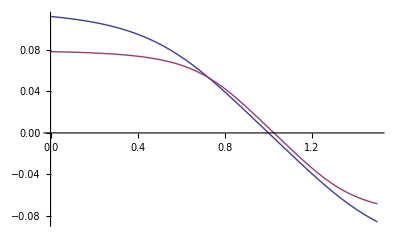

```mathematica
Plot[{ct,cp},{Jpe,0,1.5}]
```

```mathematica
b1=.;
b2=.;
g1=.;
g2=.;
ct0=.;
cp0=.;
k=.;
```

```mathematica
ct
```

((b1-b2 Jpe) (1/((1/ct0)^k+Abs[b1-b2 Jpe]^-k))^(1/k))/Abs[b1-b2 Jpe]

```mathematica
cp
```

((g1-g2 Jpe) (1/((1/cp0)^k+Abs[g1-g2 Jpe]^-k))^(1/k))/Abs[g1-g2 Jpe]

```mathematica
nmp=60 wmr1/(2 pi)
```

9.5493 wmr1

```mathematica
nsp=wmr1/(2 pi)
```

0.159155 wmr1

```mathematica
Jpe=Up/((.00001+nsp) dp)
```

Up/(dp (0.00001+0.159155 wmr1))

```mathematica
systemEquationsDA={
thrust==ct rho nsp^2 dp^4,
cmr1==(cp rho nsp^2 dp^5)/(2 pi)
};
```

```mathematica
systemVariables={thrust,cmr1}
```

{thrust,cmr1}

```mathematica
expressions={
torque==cmr1,
Zcmr1==0.,
Pin==cmr1 wmr1,
Pout==thrust Up,
Jp==Jpe
};
```

```mathematica
Compgen[file]
```

Unset::wrsym: Symbol Up is Protected.

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "AeroPropeller", "displayname" → "AeroPropeller"}, {XMLElement["icon", {"isopath" → "AeroPropeller.svg", "iconrotation" → "ON", "userpath" → "AeroPropeller.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "Pmr1"}, {}], XMLElement["portpose", {"x" → 0.333333, "y" → "0", "a" → "90", "name" → "Up"}, {}], « 4 », XMLElement["portpose", {"x" → "0.666667", "y" → "1", "a" → "90", "name" → "Pout"}, {}], XMLElement["portpose", {"x" → "0.833333", "y" → "1", "a" → "90", "name" → "Jp"}, {}]}]}] in XMLElement["hopsanobjectappearance", {« 1 »}, XMLElement["modelobject", {"typename" → "Aer" … "ler", « 1 »}, {XMLElement["icon", {"isopath" → "AeroPropeller.svg", "iconrotation" → "ON", "userpath" → "AeroPropeller.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "Pmr1"}, {}], XMLElement["portpose", {"x" → 0.333333, "y" → "0", "a" → "90", "name" → "Up"}, {}], « 4 », XMLElement["portpose", {"x" → "0.666667", "y" → "1", "a" → "90", "name" → "Pout"}, {}], XMLElement["portpose", {"x" → "0.833333", "y" → "1", "a" → "90", "name" → "Jp"}, {}]}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "x" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.666667 in "x" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

AeroPropeller.xml

## Combustion Chamber Monopropellant

```mathematica
domain="Aero";
displayName="CombustionChamberMono";
author="Petter Krus <petter.krus@liu.se>";
brief="Hydraulic volume with two connection";
componentType="ComponentC";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

### Model

```mathematica
componentName = StringJoin[domain,displayName];
file = ToString[StringJoin[componentName,".hpp"]];
componentGroup = StringJoin[domain,"Components"];
```

```mathematica
nodeConnections={
	HydraulicCnode[1,1.*10^5,"Upstream port"]
};
```

```mathematica
inputVariables={
{p0,1.0*10^5,double," ","Free stream pressure"}
};
```

```mathematica
inputParameters={
{Vc,1.0*10^3,double," ","Chamber volume"},
{R,287,double,"","Gas constant"},
{cv,718,double,"","Heat capacity"},
{vfuel,1000.,double,"m/s","Exhaust speed"},
{ethap,0.9,double,"","Effectivness"},
{rhofuel,900.,double,"kg/m3","Exhaust speed"},
{As,0.01,double,"m2","min effective area"},
{Med,2.5,double,"","Design exit Mach"},
{alpha,0.0,double,"1/s ","Damp. factor"}
};
```

```mathematica
outputVariables={
{thrust,0.,double,"m3/s","thrust"},
{Tt,273.,double,"K","cahmber temerature"},
{mc,0.,double,"kg","mass in chamber"},
{mdot,0.,double,"kg/s","Exit mass flow"},
{Ae,0.,double,"","exit Mach number"},
{pe,0.,double,"Pa","exit pressure"},
{pt,0.,double,"Pa","chamber pressure"},
{Te,273.,double,"K","exit temperature"},
{ve,0.,double,"K","exit velocity"},
{Pin,0.,double,"W","Input power"},
{Pout,0.,double,"W","Output power"}
};
```

```mathematica
γ=gam;
```

```mathematica
initialExpressions={
c1==p1,
c2==p1,
pt==p1,
c1f==p1,
c2f==p1,
Tt==T1;
mc ==(pt Vc)/(R Tt)
};
```

```mathematica
cfuel= vfuel^2/2;
```

```mathematica
Cep=γ Vc
```

gam Vc

```mathematica
mdot1=q1 rhofuel;
q1E=q1 rhofuel (cfuel+cv T1);
mdot2=-mdot;
```

```mathematica
Zc1e=(mTimestep (cfuel+cv T1) rhofuel)/Cep
```

(mTimestep rhofuel (cv T1+vfuel^2/2))/(gam Vc)

```mathematica
ZcEp=mTimestep/Cep
```

mTimestep/(gam Vc)

```mathematica
qE1=mdot1 cfuel
```

1/2 q1 rhofuel vfuel^2

```mathematica
qE2 =-mdot (ve^2/2+(R+cv)Te);
```

```mathematica
localExpressions={
γ==(cv+R)/cv,
Ae==As((γ+1)/2)^(-(γ+1)/(2(γ-1)))((1+(γ-1)/2 Med^2)^((γ+1)/(2(γ-1))))/Med

};
```

```mathematica
systemEquationsDA={
der[mc]==(mdot1+mdot2),
mc R Tt == pt Vc,
pt==c2+ZcEp qE2,
mdot==((As pt)/(√Tt)√(γ/R)((γ+1)/2)^(-(γ+1)/(2(γ-1)))),
Te==Tt(1+(γ-1)/2 Me^2)^-1,
ve==Me √(γ R Te)
};
```

```mathematica
systemVariables={mc,Tt,pt,mdot,Te,ve};
```

```mathematica
variableLimits={
{mdot,0.,1. 10^9}
};
```

```mathematica
Me=Med;
```

```mathematica
expressions={
c10==c2+2 ZcEp qE2,
c20==c1+2 Zc1e q1,
c1==c1f,
c2==c2f,
c1f==alpha c1f +(1.0-alpha) c10,
c2f==alpha c2f +(1.0-alpha) c20,
pe==pt(1+(γ-1)/2 Me^2)^(-γ/(γ-1)),
thrust==(mdot ve+Ae(pe-p0)),
Zc1==Zc1e,
Pin==mdot1 cfuel,
Pout==mdot2 ve^2/2
};
```

expressions={
{ve,(Me*sqrt (gam*R*Te))},
{thrust,(mdot vfuel+Ae(pe-p0))},
{c1,c1f},
{c2,c2f},
{c1f,alpha c1f +(1.0-alpha) c10},
{c2f,alpha c2f +(1.0-alpha) c20},
{Zc1,Zc1e},
{pt,c2+ZcEp q2E},
{Pin,mdot1 cfuel},
{Pout,-mdo2 ve^2/2}
};

```mathematica
Compgen[file]
```

Part::partd: Part specification delayedPart ⟦ 1, 1 ⟧ is longer than depth of object.

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "AeroCombustionChamberMono", "d" … "e" → "" … ""}, {XMLElement["icon", {"isopath" → "AeroCombustionChamberMono.svg", "iconrotation" → "ON", "userpath" → "AeroCombustionChamberMono.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "P1"}, {}], XMLElement["portpose", {"x" → 0.5, "y" → "0", "a" → "90", "name" → "p0"}, {}], « 9 », XMLElement["portpose", {"x" → "0.833333", "y" → "1", "a" → "90", "name" → "Pin"}, {}], XMLElement["portpose", {"x" → "0.916667", "y" → "1", "a" → "90", "name" → "Pout"}, {}]}]}] in XMLElement["hopsanobjectappearance", « 1 », XMLElement["modelobject", {"" … "e" → "" … "", « 1 »}, {XMLElement["icon", {"isopath" → "AeroCombustionChamberMono.svg", "iconrotation" → "ON", "userpath" → "AeroCombustionChamberMono.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "P1"}, {}], XMLElement["portpose", {"x" → 0.5, "y" → "0", "a" → "90", "name" → "p0"}, {}], « 9 », XMLElement["portpose", {"x" → "0.833333", "y" → "1", "a" → "90", "name" → "Pin"}, {}], XMLElement["portpose", {"x" → "0.916667", "y" → "1", "a" → "90", "name" → "Pout"}, {}]}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "x" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

AeroCombustionChamberMono.xml

```mathematica
expressions
```

{c10==c2-(2 mdot mTimestep ((cv+R) Te+ve^2/2))/(gam Vc),c20==c1+(2 mTimestep q1 rhofuel (cv T1+vfuel^2/2))/(gam Vc),c1==c1f,c2==c2f,c1f==(1.-alpha) c10+alpha c1f,c2f==(1.-alpha) c20+alpha c2f,pe==(1+1/2 (-1+gam) Med^2)^(-gam/(-1+gam)) pt,thrust==Ae (-p0+pe)+mdot ve,Zc1==(mTimestep rhofuel (cv T1+vfuel^2/2))/(gam Vc),Pin==1/2 q1 rhofuel vfuel^2,Pout==-(mdot ve^2)/2}

## Atmosphere

```mathematica
domain="Aero";
displayName="Atmosphere";
brief="model of standard atmosphere";
componentType="ComponentSignal";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[];
```

```mathematica
inputVariables={{ha,0.,double,"m","Altitude"}};
```

```mathematica
inputParameters={{g0,9.81,double,"m/s^2","Gravitation acceleration"},{rhos,1.225,double,"kg/m3","Density at sea level"},
{a,-0.0065,double,"",""},
{R,287,double,"",""},
{gamma,1.4,double,"",""},
{Ts,288.16,double,"K","Temperature at sea level"},
{p0s,101300.,double,"Pa",""},
{htp,11000.,double,"m","Onset of tropopaus"},
{Ttp,216.66,double,"K",""},
{ptp,22610.,double,"Pa",""},
{rhotp,0.363649,double,"kg/m3",""},
{e,N[E,6],double,"","e"}};
```

```mathematica
outputVariables={
{rho,1.25,double,"kg/m3","The density at altitude h"},
{T,273.,double,"K","Temperature at altitude h"},
{p0,100000.,double,"Pa","Pressure at altitude h"},
{Vsound,340.,double,"m/s","Speed of sound at altitude h"}
};
```

```mathematica
Ta:=onNegative[ha-htp] (Ts+a ha)+onPositive[ha-htp] (Ts+a htp)
```

```mathematica
p0a:=onNegative[ha-htp] p0s*(Ta/Ts)^(-(g0/(a R)))+onPositive[ha-htp] ptp*e^(-(g0/(R Ttp)) (ha-htp))
```

```mathematica
rhoa1:=rhos*(Ta1/Ts)^(-((g0/(a R)+1)))
```

```mathematica
rhoa:=onNegative[ha-htp] rhos*(Ta/Ts)^(-((g0/(a R)+1)))+onPositive[ha-htp] rhotp*e^(-(g0/(R Ttp))(ha-htp))
```

```mathematica
Vsounda:=Sqrt[gamma R Ta]
```

```mathematica
expressions={
rho==rhoa,
T==Ta,
p0==p0a,
Vsound==Vsounda
};
```

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "Ae" … "re", « 1 »}, {XMLElement["icon", {"isopath" → "AeroAtmosphere.svg", "iconrotation" → "ON", "userpath" → "AeroAtmosphere.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → 0.5, "y" → "0", "a" → "90", "name" → "ha"}, {}], XMLElement["portpose", {"x" → "0.2", "y" → "1", "a" → "90", "name" → "rho"}, {}], XMLElement["portpose", {"x" → "0.4", "y" → "1", "a" → "90", "name" → "T"}, {}], XMLElement["portpose", {"x" → "0.6", "y" → "1", "a" → "90", "name" → "p0"}, {}], XMLElement["portpose", {"x" → "0.8", "y" → "1", "a" → "90", "name" → "Vsound"}, {}]}]}] in XMLElement["hopsanobjectappearance", « 1 », XMLElement["modelobject", {"typename" → "" … "", « 1 »}, {XMLElement["icon", {"isopath" → "AeroAtmosphere.svg", "iconrotation" → "ON", "userpath" → "AeroAtmosphere.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → 0.5, "y" → "0", "a" → "90", "name" → "ha"}, {}], XMLElement["portpose", {"x" → "0.2", "y" → "1", "a" → "90", "name" → "rho"}, {}], XMLElement["portpose", {« 1 »}, {}], XMLElement["portpose", {"x" → "0.6", "y" → "1", "a" → "90", "name" → "p0"}, {}], XMLElement["portpose", {"x" → "0.8", "y" → "1", "a" → "90", "name" → "Vsound"}, {}]}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "x" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

AeroAtmosphere.xml

```mathematica
g0 = 9.81;
rhos = 1.225;
a = -0.0065;
R = 287;
Ts = 288.16;
p0s = 101300;
gamma = 1.4;
htp =11000;
Ttp = 216.66;
ptp = 22610;
rhotp=0.363649;
```

```mathematica
onPositive[x_]:=(Sign[x]+1)/2
```

```mathematica
onNegative[x_]:=1-onPositive[x]
```

Plot::exclul: {Im[e] - 0, (-11000 + Re[ha]) - 0, (-11000 + Re[ha]) - 0, (-11000 + Re[ha]) - 0, (-11000 + Re[ha]) - 0, (Im[(288.16  - 0.0065\ ha)\ (1 + 1/2\ Plus[« 2 »])] + 108.33\ Im[Sign[-11000 + ha]]) - 0}
 must be a list of equalities or real-valued functions.

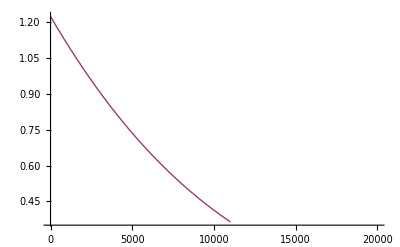

```mathematica
Plot[{rhoa1,rhoa},{ha,1,20000}]
```

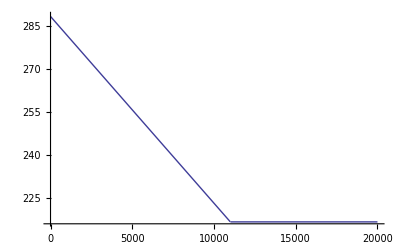

```mathematica
Plot[Ta,{ha,1,20000}]
```

Plot::exclul: {Im[e] - 0, (-11000 + Re[ha]) - 0, (-11000 + Re[ha]) - 0, (-11000 + Re[ha]) - 0, (-11000 + Re[ha]) - 0, (Im[(288.16  - 0.0065\ ha)\ (1 + 1/2\ Plus[« 2 »])] + 108.33\ Im[Sign[-11000 + ha]]) - 0}
 must be a list of equalities or real-valued functions.

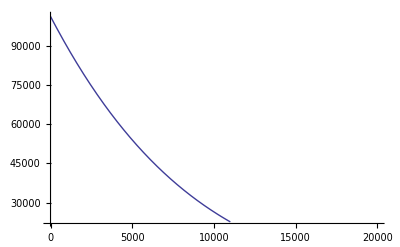

```mathematica
Plot[{p0a},{ha,1,20000}]
```

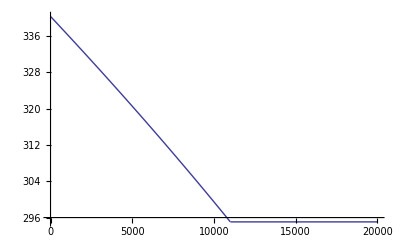

```mathematica
Plot[Vsounda,{ha,1,20000}]
```

```mathematica
g0 =.;
rhos = .;
a =.;
R =.;
Ts =.;
p0s =.;
gamma =.;
htp =.;
Ttp = .;
ptp = .;
rhotp=.;
onPositive[x_]=.;
onNegative[x_]=.;
```

# Partial Aero Components

## FlightRecorder

```mathematica
domain="Aero";
displayName="FlightRecorder";
brief="Generates a flight path for .kml for Google earth";
componentType="ComponentSignal";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[defaultPath,domain,displayName];
ResetComponentVariables[]
```

```mathematica
inputVariables={
{longitude,0.,double,"deg","longitude"},
{lattitude,0.,double,"deg","lattitude"},
{altitude,0.,double,"m","altitude"},
{phi,0.,double,"rad","roll angle"},
{theta,0.,double,"rad","tip angle"},
{psi,0.,double,"rad","yaw angle"},
{timeE,0.,double,"rad","Effective time"}
};
```

```mathematica
inputParameters={
{altitudeScale,20.0,double,"","Scaling of altitude"},
{timeStepRec,10.,double,"sec","time step for recording"}
};
```

```mathematica
outputVariables={
{scaledAltitude,0.,double,"","Scaling of altitude"}
};
```

```mathematica
expressions={
scaledAltitude==altitudeScale*altitude
}
```

{scaledAltitude==altitude altitudeScale}

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", « 1 », {XMLElement["icon", {"isopath" → "AeroFlightRecorder.svg", "iconrotation" → "ON", "userpath" → "AeroFlightRecorder.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → 0.125, "y" → "0", "a" → "90", "name" → "longitude"}, {}], XMLElement["portpose", {"x" → 0.25, "y" → "0", "a" → "90", "name" → "lattitude"}, {}], « 4 », XMLElement["portpose", {"x" → 0.875, "y" → "0", "a" → "90", "name" → "timeE"}, {}], XMLElement["portpose", {"x" → "0.5", "y" → "1", "a" → "90", "name" → "scaledAltitude"}, {}]}]}] in XMLElement["hopsanobjectappearance", « 1 », XMLElement["modelobject", {"t" … "e" → "" … "", « 1 »}, {XMLElement["icon", {"isopath" → "AeroFlightRecorder.svg", "iconrotation" → "ON", "userpath" → "AeroFlightRecorder.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → 0.125, "y" → "0", "a" → "90", "name" → "longitude"}, {}], XMLElement["portpose", {"x" → 0.25, "y" → "0", "a" → "90", "name" → "lattitude"}, {}], « 4 », XMLElement["portpose", {"x" → 0.875, "y" → "0", "a" → "90", "name" → "timeE"}, {}], XMLElement["portpose", {"x" → "0.5", "y" → "1", "a" → "90", "name" → "scaledAltitude"}, {}]}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.125 in "x" → 0.125 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.25 in "x" → 0.25 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.375 in "x" → 0.375 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

AeroFlightRecorder.xml